## p10q3

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
gapedgefind[d_]:=Min[Abs[d]]-10^(-6);
leftfind[d_]:=(Transpose@Position[d,_?(#<0&)])[[1]];
rightfind[d_]:=(Transpose@Position[d,_?(#>0&)])[[1]];
```

```mathematica
datadir="/home/cal422/PycharmProjects/Hyperbolic_Lattice_Self_Consistent_Hartree_Fock_Data_Acquisition/Mathematica_Final_Plots/Final_Data_Magnetic_Catalysis_Final_Paper_Figures/6_DOS_InteractionGap_AFM";
```

```mathematica
a0b1u0d8data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0_amag1_U0.8_eigvals.txt"],"Data"])[[1]]]];
a0d6b1u0d8data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.6_amag1_U0.8_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
a0b1u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0_amag1.0_V0_eigvals.txt"],"Data"])[[1]]]];
a0d6b1u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.6_amag1.0_V0_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
a0b0u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0_amag0_V0_eigvals.txt"],"Data"])[[1]]]];
a0d6b0u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p10q3n4a0.6_amag0_V0_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
linethickness=0.006;
```

```mathematica
xrange={-3,3};
yrange={0,0.8};
```

71

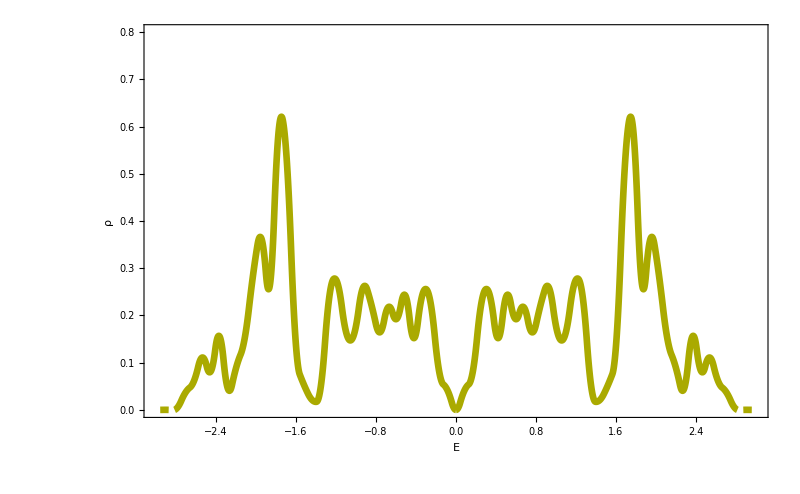

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0b0u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0b0u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0b0u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Yellow],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

71

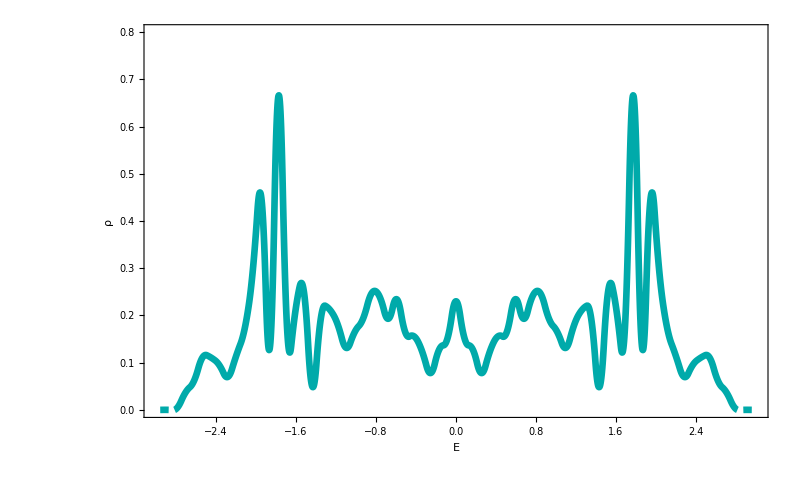

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0b1u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0b1u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0b1u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Cyan],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

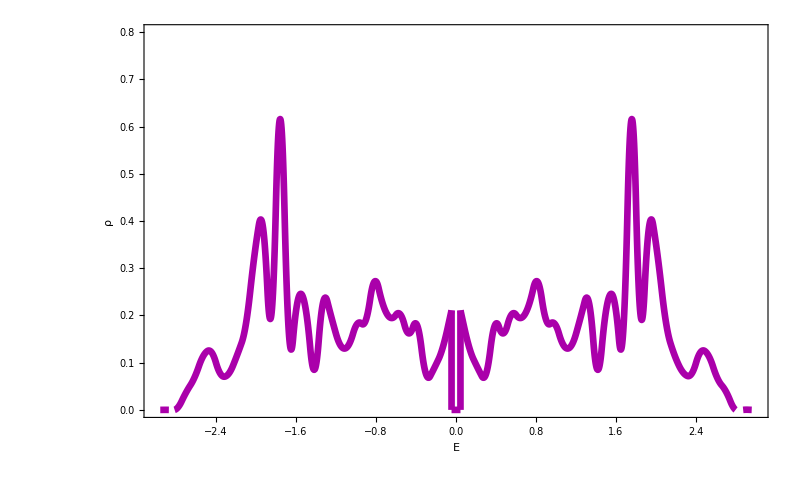

```mathematica
datasize=Length[a0b1u0d8data]; (**)

gapedge=gapedgefind[a0b1u0d8data]; (**)
leftdata=a0b1u0d8data[[leftfind[a0b1u0d8data]]];(**)
rightdata=a0b1u0d8data[[rightfind[a0b1u0d8data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0b1u0d8hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

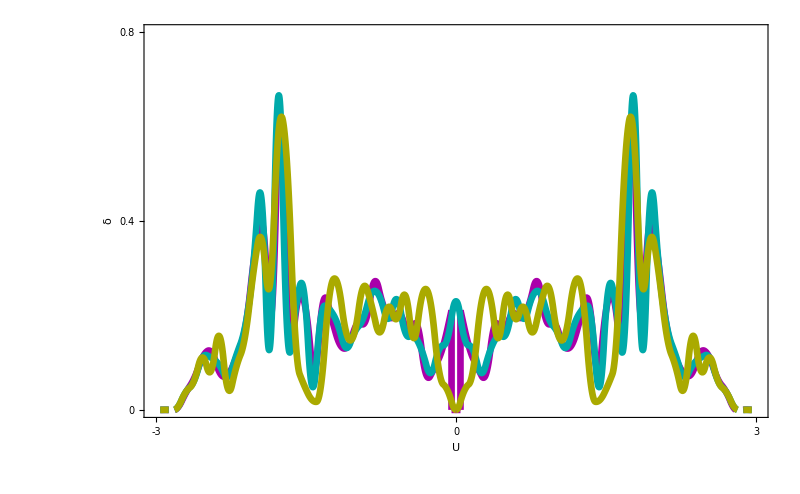

```mathematica
Show[
a0b1u0d8hist,a0b1u0hist,a0b0u0hist,
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.4,0.8},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

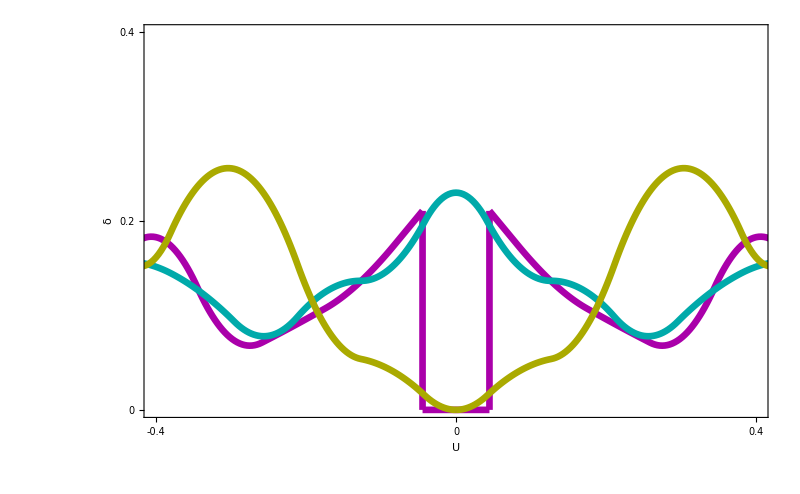

```mathematica
Show[
a0b1u0d8hist,a0b1u0hist,a0b0u0hist,
PlotRange->{{-0.4,0.4},{0,0.4}},
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.2,0.4},None},{{-0.4,0,0.4},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
xrange={-3,3};
yrange={0,1};
```

81

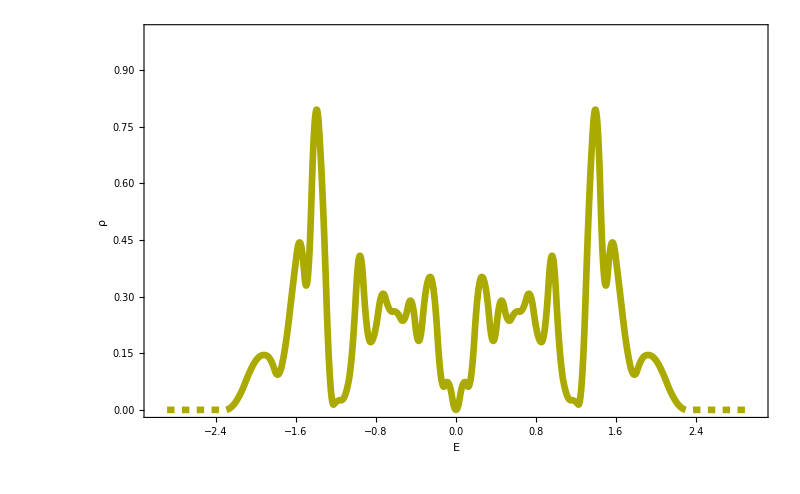

```mathematica
bw=(3-(-3))/81;
binedges= HistogramList[a0d6b0u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d6b0u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d6b0u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Yellow],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

81

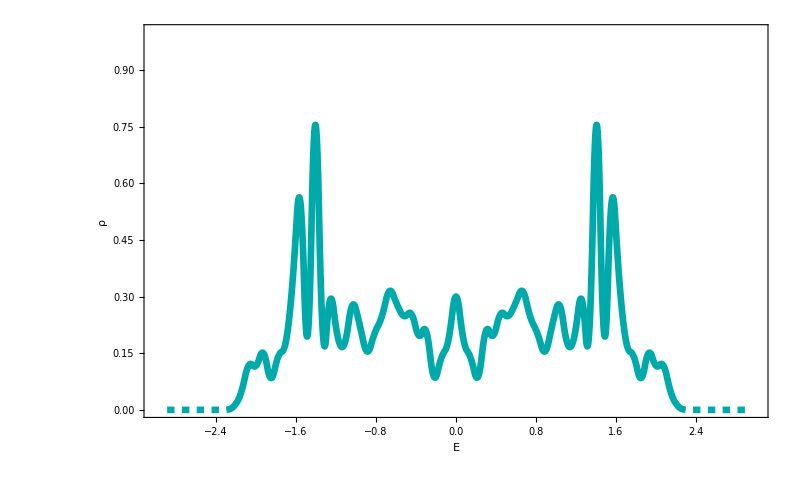

```mathematica
bw=(3-(-3))/81;
binedges= HistogramList[a0d6b1u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d6b1u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d6b1u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Cyan],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

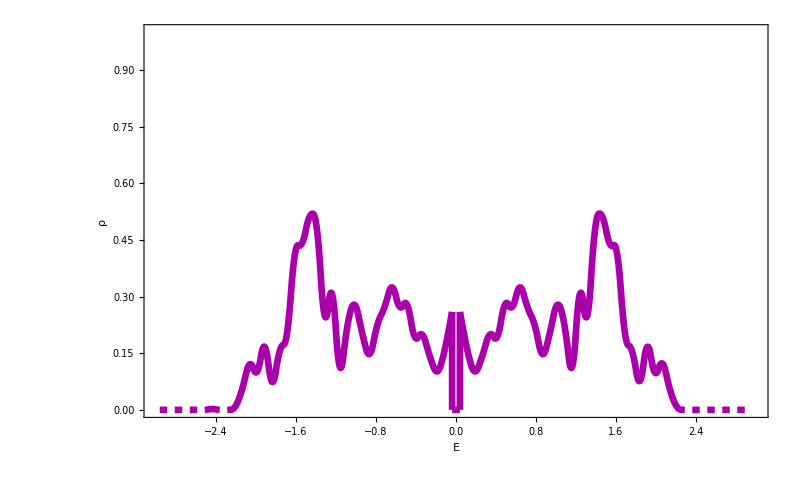

```mathematica
datasize=Length[a0d6b1u0d8data]; (**)

gapedge=gapedgefind[a0d6b1u0d8data]; (**)
leftdata=a0d6b1u0d8data[[leftfind[a0d6b1u0d8data]]];(**)
rightdata=a0d6b1u0d8data[[rightfind[a0d6b1u0d8data]]];(**)

numbergappoints=50;
numberbins=81;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d6b1u0d8hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

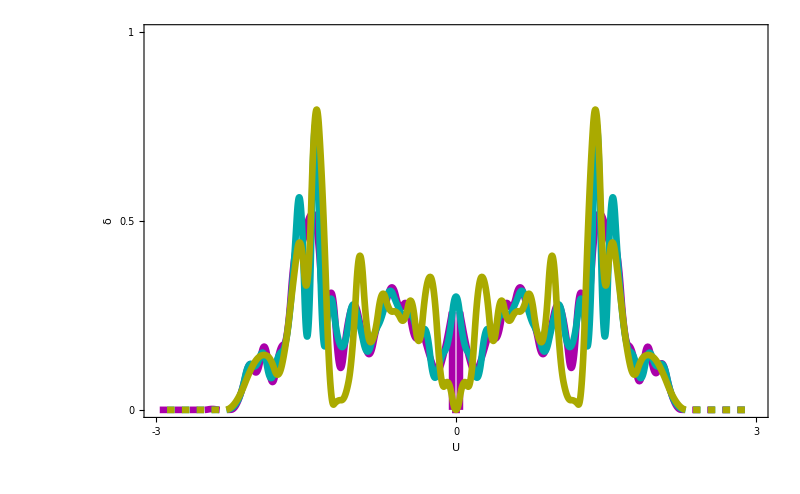

```mathematica
Show[
a0d6b1u0d8hist,a0d6b1u0hist,a0d6b0u0hist,
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.5,1},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

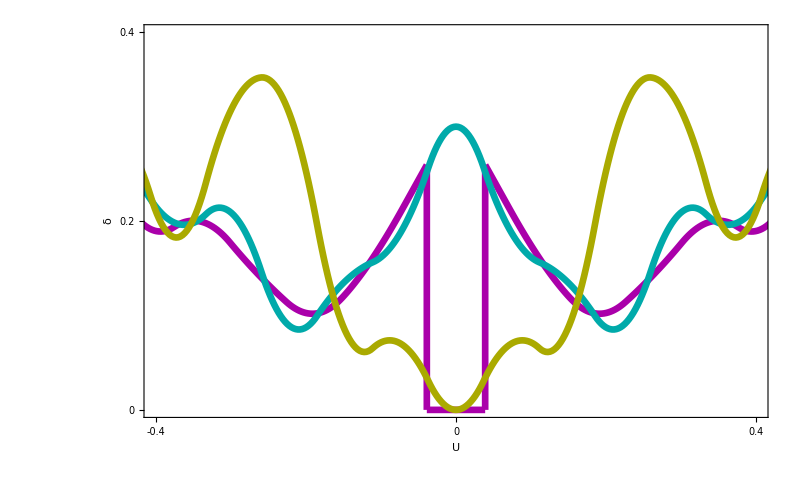

```mathematica
Show[
a0d6b1u0d8hist,a0d6b1u0hist,a0d6b0u0hist,
PlotRange->{{-0.4,0.4},{0,0.4}},
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.2,0.4},None},{{-0.4,0,0.4},None}},FrameTicksStyle->FontSize->50
]
```

## p14q3

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
gapedgefind[d_]:=Min[Abs[d]]-10^(-6);
leftfind[d_]:=(Transpose@Position[d,_?(#<0&)])[[1]];
rightfind[d_]:=(Transpose@Position[d,_?(#>0&)])[[1]];
```

```mathematica
datadir="/home/cal422/PycharmProjects/Hyperbolic_Lattice_Self_Consistent_Hartree_Fock_Data_Acquisition/Mathematica_Final_Plots/Final_Data_Magnetic_Catalysis_Final_Paper_Figures/6_DOS_InteractionGap_AFM";
```

```mathematica
a0b1u0d7data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0_amag1_U0.7_eigvals.txt"],"Data"])[[1]]]];
a0d7b1u0d7data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.7_amag1_U0.7_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
a0b1u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0_amag1.0_V0_eigvals.txt"],"Data"])[[1]]]];
a0d7b1u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.7_amag1.0_U0_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
a0b0u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0_amag0_V0_eigvals.txt"],"Data"])[[1]]]];
a0d7b0u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/p14q3n3a0.7_amag0_U0_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
linethickness=0.006;
```

```mathematica
xrange={-3,3};
yrange={0,0.8};
```

71

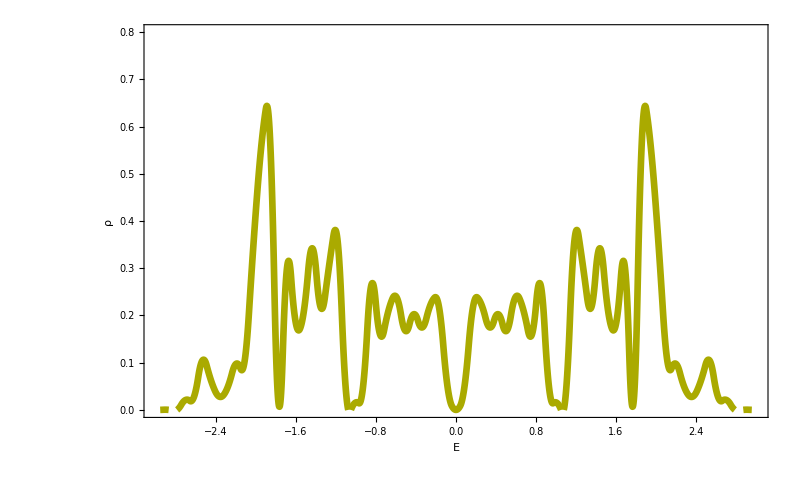

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0b0u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0b0u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0b0u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Yellow],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

71

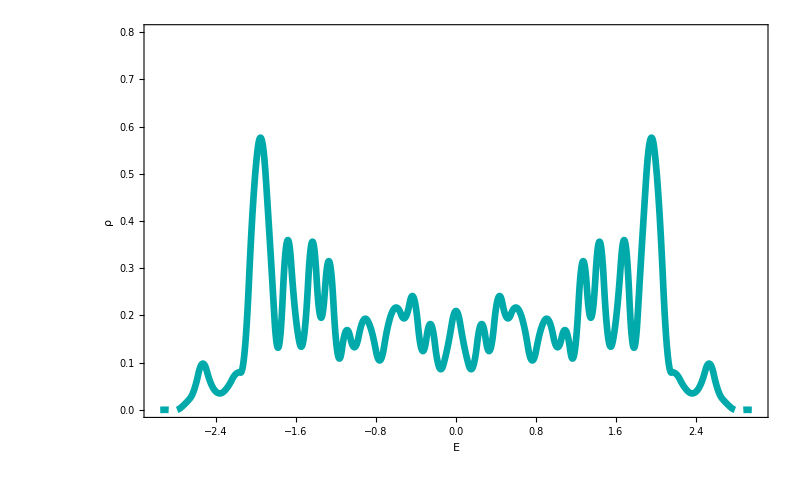

```mathematica
bw=(3-(-3))/71;
binedges= HistogramList[a0b1u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0b1u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0b1u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Cyan],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

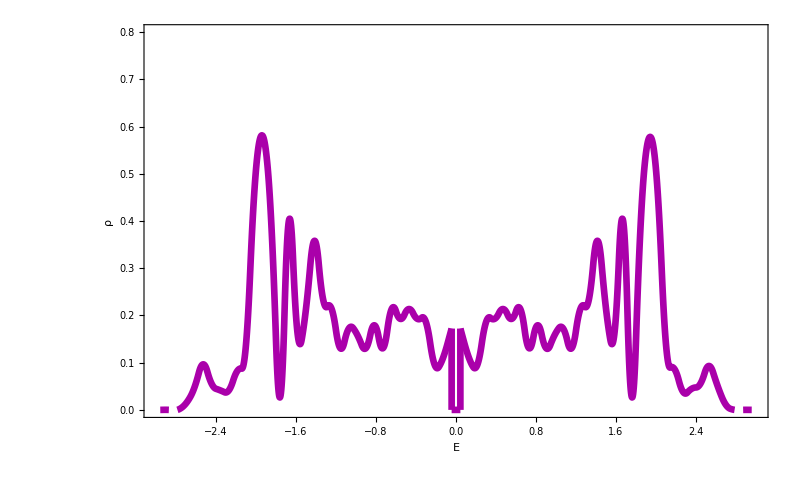

```mathematica
datasize=Length[a0b1u0d7data]; (**)

gapedge=gapedgefind[a0b1u0d7data]; (**)
leftdata=a0b1u0d7data[[leftfind[a0b1u0d7data]]];(**)
rightdata=a0b1u0d7data[[rightfind[a0b1u0d7data]]];(**)

numbergappoints=50;
numberbins=71;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0b1u0d7hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

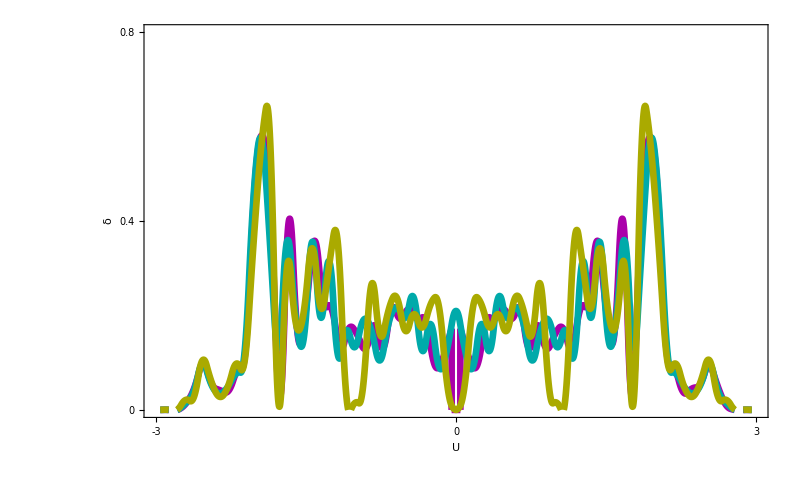

```mathematica
Show[
a0b1u0d7hist,a0b1u0hist,a0b0u0hist,
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.4,0.8},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

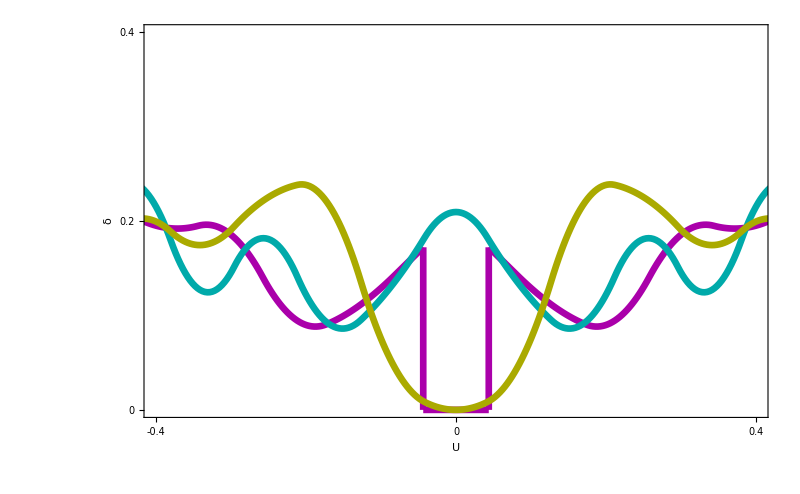

```mathematica
Show[
a0b1u0d7hist,a0b1u0hist,a0b0u0hist,
PlotRange->{{-0.4,0.4},{0,0.4}},
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.2,0.4},None},{{-0.4,0,0.4},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
xrange={-3,3};
yrange={0,1.2};
```

81

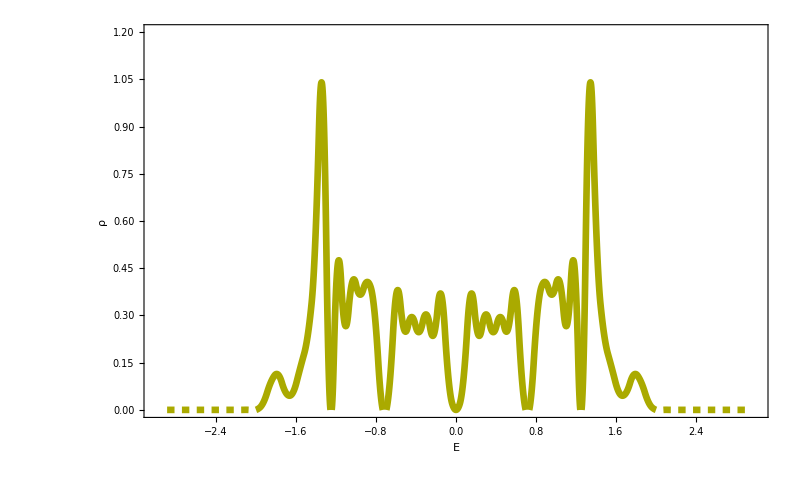

```mathematica
bw=(3-(-3))/81;
binedges= HistogramList[a0d7b0u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d7b0u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d7b0u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Yellow],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

81

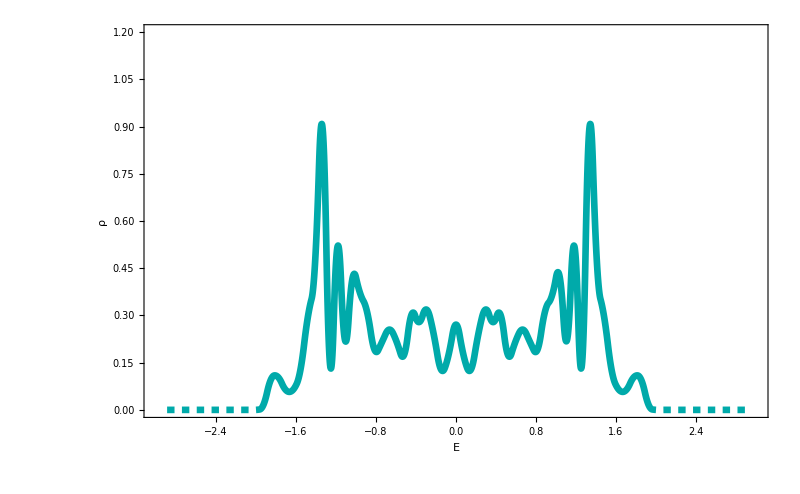

```mathematica
bw=(3-(-3))/81;
binedges= HistogramList[a0d7b1u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d7b1u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d7b1u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Cyan],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

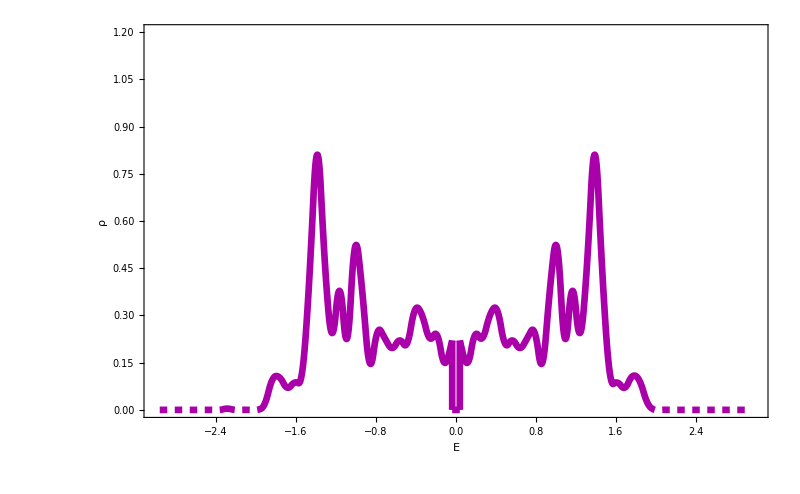

```mathematica
datasize=Length[a0d7b1u0d7data]; (**)

gapedge=gapedgefind[a0d7b1u0d7data]; (**)
leftdata=a0d7b1u0d7data[[leftfind[a0d7b1u0d7data]]];(**)
rightdata=a0d7b1u0d7data[[rightfind[a0d7b1u0d7data]]];(**)

numbergappoints=50;
numberbins=81;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d7b1u0d7hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

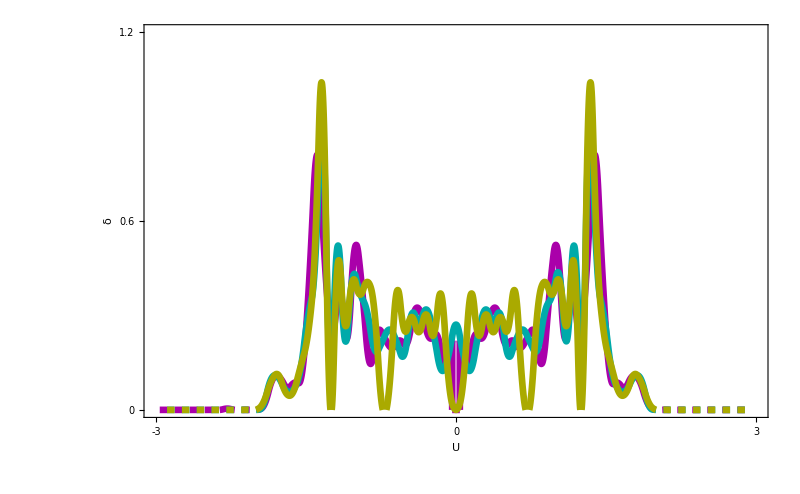

```mathematica
Show[
a0d7b1u0d7hist,a0d7b1u0hist,a0d7b0u0hist,
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.6,1.2},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

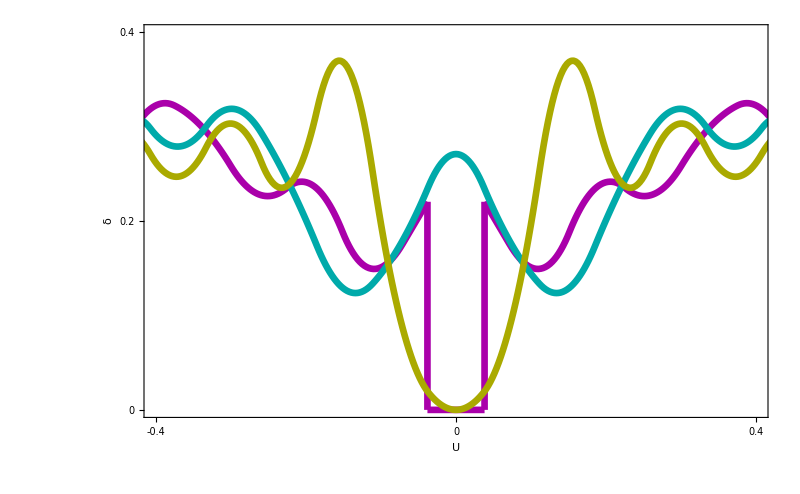

```mathematica
Show[
a0d7b1u0d7hist,a0d7b1u0hist,a0d7b0u0hist,
PlotRange->{{-0.4,0.4},{0,0.4}},
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.2,0.4},None},{{-0.4,0,0.4},None}},FrameTicksStyle->FontSize->50
]
```

## Honeycomb

```mathematica
cstn[x_]:=ToExpression[StringDelete[StringReplace[x,{"e+"->"*10^","e-"->"*10^-","j"->"I"}],{"(",")"}]];
gapedgefind[d_]:=Min[Abs[d]]-10^(-6);
leftfind[d_]:=(Transpose@Position[d,_?(#<0&)])[[1]];
rightfind[d_]:=(Transpose@Position[d,_?(#>0&)])[[1]];
```

```mathematica
datadir="/home/cal422/PycharmProjects/Hyperbolic_Lattice_Self_Consistent_Hartree_Fock_Data_Acquisition/Mathematica_Final_Plots/Final_Data_Magnetic_Catalysis_Final_Paper_Figures/6_DOS_InteractionGap_AFM";
```

```mathematica
a0b0d5u1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0_amag0.5_U1_eigvals.txt"],"Data"])[[1]]]];
a0d8b0d5u1data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombOBC_nl20a0.8_amag0.5_U1_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
a0b0d5u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycomb_nl20_openBC_a0amag0d5_V0_eigvals.txt"],"Data"])[[1]]]];
a0d8b0d5u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycomb_nl20_openBC_a0.8amag0d5_V0_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
a0b0u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombPBC_nl20a0_amag0_V0_eigvals.txt"],"Data"])[[1]]]];
a0d8b0u0data=Re[Map[cstn,(Transpose@Import[StringJoin[datadir,"/honeycombPBC_nl20a0.8_amag0_V0_eigvals.txt"],"Data"])[[1]]]];
```

```mathematica
linethickness=0.006;
```

```mathematica
xrange={-3,3};
yrange={0,0.6};
```

50

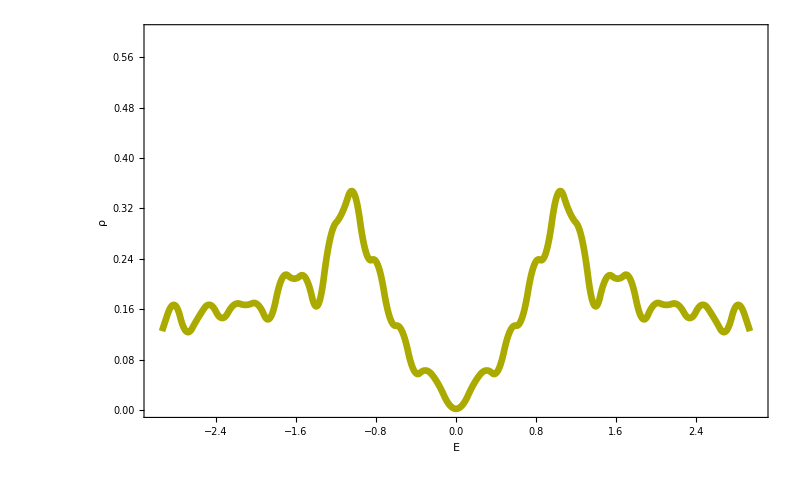

```mathematica
bw=(3-(-3))/50;
binedges= HistogramList[a0b0u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0b0u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0b0u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Yellow],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

50

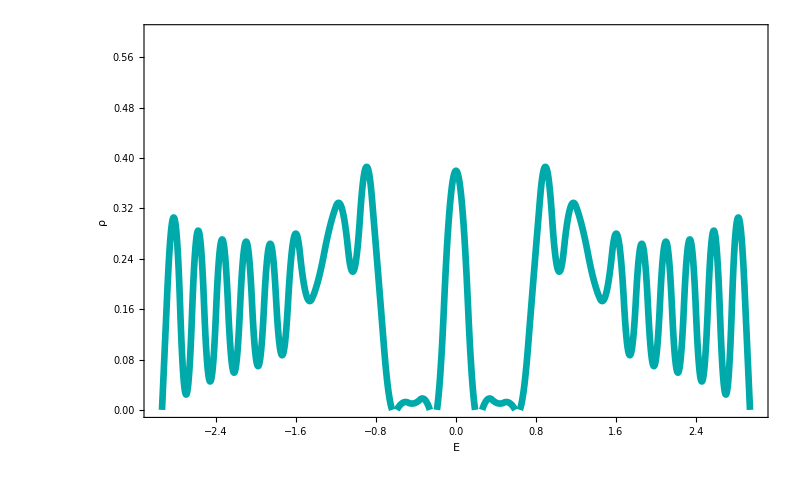

```mathematica
bw=(3-(-3))/50;
binedges= HistogramList[a0b0d5u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0b0d5u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0b0d5u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Cyan],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

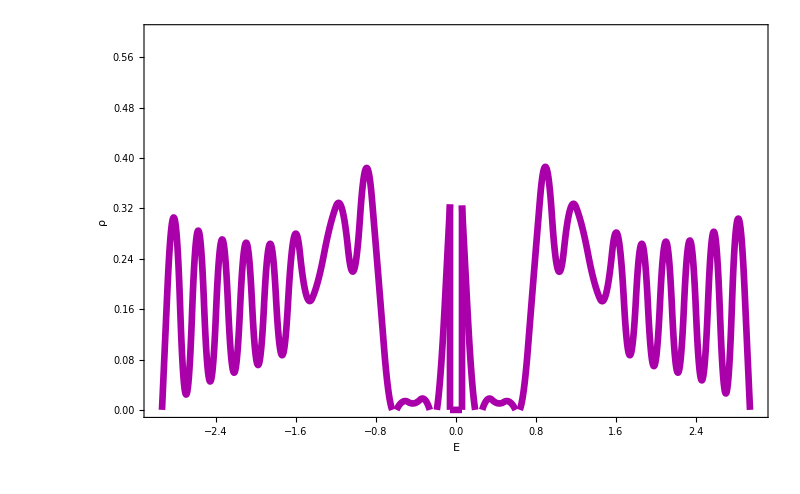

```mathematica
datasize=Length[a0b0d5u1data]; (**)

gapedge=gapedgefind[a0b0d5u1data]; (**)
leftdata=a0b0d5u1data[[leftfind[a0b0d5u1data]]];(**)
rightdata=a0b0d5u1data[[rightfind[a0b0d5u1data]]];(**)

numbergappoints=50;
numberbins=51;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0b0d5u1hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

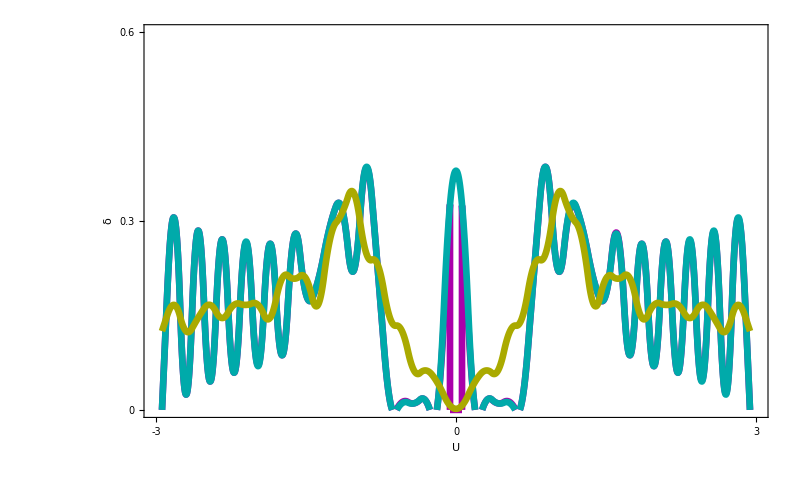

```mathematica
Show[
a0b0d5u1hist,a0b0d5u0hist,a0b0u0hist,
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.3,0.6},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

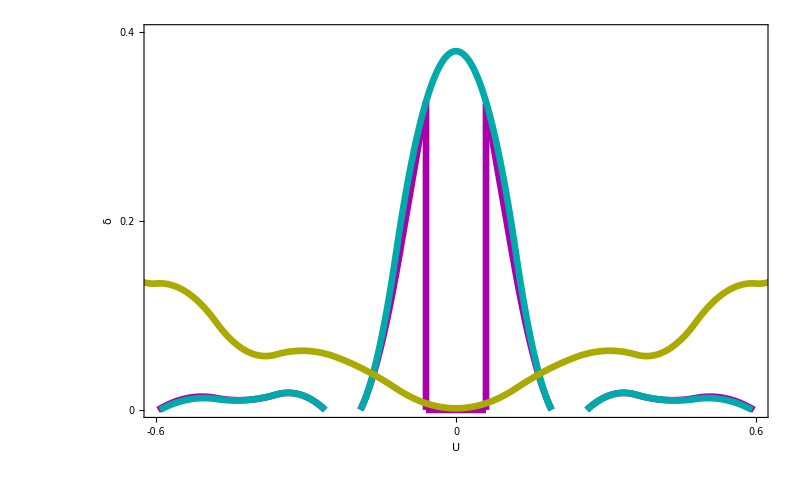

```mathematica
Show[
a0b0d5u1hist,a0b0d5u0hist,a0b0u0hist,
PlotRange->{{-0.6,0.6},{0,0.4}},
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.2,0.4},None},{{-0.6,0,0.6},None}},FrameTicksStyle->FontSize->50
]
```

```mathematica
xrange={-3,3};
yrange={0,0.8};
```

60

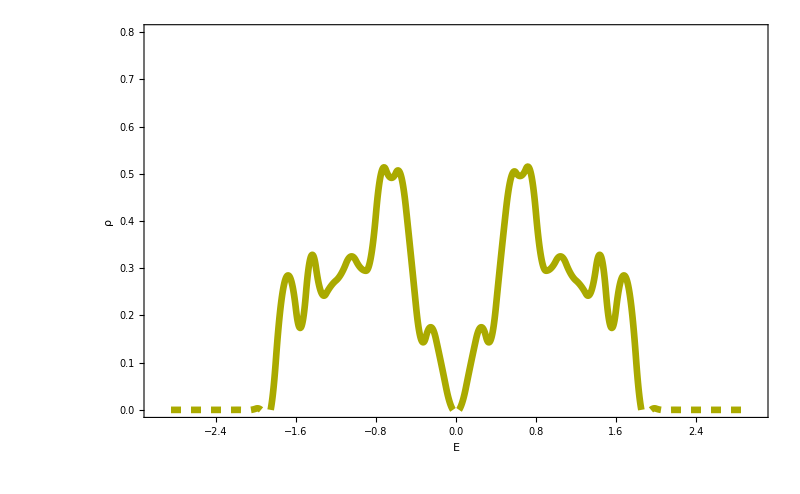

```mathematica
bw=(3-(-3))/60;
binedges= HistogramList[a0d8b0u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d8b0u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d8b0u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Yellow],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

60

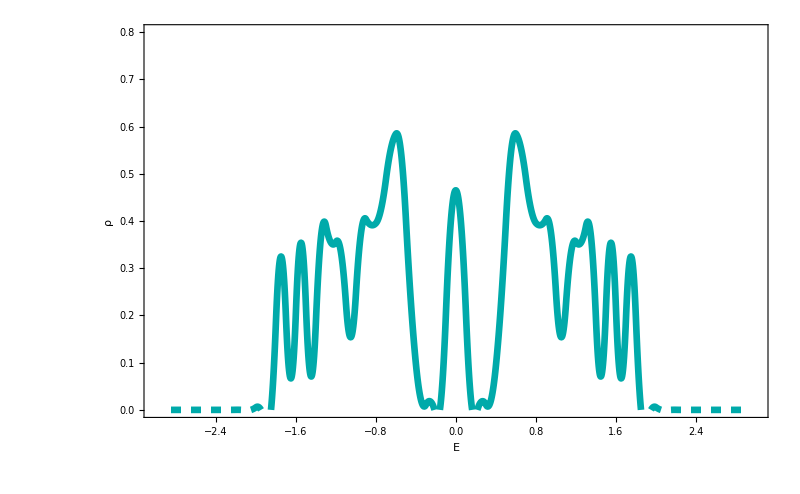

```mathematica
bw=(3-(-3))/60;
binedges= HistogramList[a0d8b0d5u0data,{-3,3,bw},Count][[1]]; (**)
bincenters=binedges+0.5*bw;
bincenters= bincenters[[1;;Length[bincenters]-1]];
Length[bincenters]
counts=HistogramList[a0d8b0d5u0data,{-3,3,bw},Count][[2]]; (**)
counts=counts/Total[counts]/bw;
a0d8b0d5u0hist=Show[ListPlot[Transpose@{bincenters,counts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Cyan],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"E","ρ"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

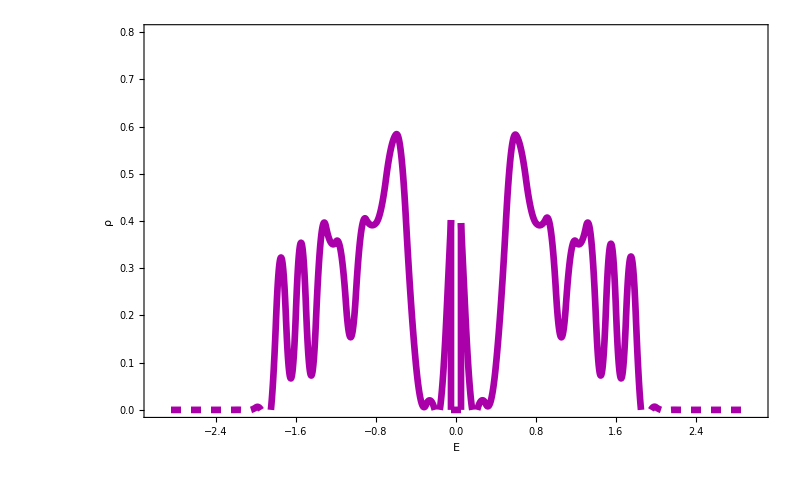

```mathematica
datasize=Length[a0d8b0d5u1data]; (**)

gapedge=gapedgefind[a0d8b0d5u1data]; (**)
leftdata=a0d8b0d5u1data[[leftfind[a0d8b0d5u1data]]];(**)
rightdata=a0d8b0d5u1data[[rightfind[a0d8b0d5u1data]]];(**)

numbergappoints=50;
numberbins=61;
bw=(3-gapedge)/((numberbins-1)/2);
leftbinedges=Subdivide[-3,-gapedge,(numberbins-1)/2];
rightbinedges=Subdivide[gapedge,3,(numberbins-1)/2];
leftbincenters=(leftbinedges+0.5*bw)[[;;-2]];
rightbincenters=(rightbinedges+0.5*bw)[[;;-2]];
gapbincenters=Subdivide[leftbincenters[[-1]],rightbincenters[[1]],numbergappoints-1];

leftcounts=BinCounts[leftdata,{leftbinedges}]/datasize/bw;
rightcounts=BinCounts[rightdata,{rightbinedges}]/datasize/bw;
gapcounts=ConstantArray[0,numbergappoints];

bincenters=Join[leftbincenters,gapbincenters,rightbincenters];
counts=Join[leftcounts,gapcounts,rightcounts];

a0d8b0d5u1hist=Show[
ListPlot[Transpose@{leftbincenters,leftcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{rightbincenters,rightcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{gapbincenters,gapcounts},Joined->True,InterpolationOrder->2,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{leftbincenters[[-1]],gapbincenters[[1]]},{leftcounts[[-1]],gapcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
ListPlot[Transpose@{{gapbincenters[[-1]],rightbincenters[[1]]},{gapcounts[[-1]],rightcounts[[1]]}},Joined->True,InterpolationOrder->1,PlotStyle->{Darker[Magenta],Thickness->linethickness},PlotRange->{xrange,yrange}],
BaseStyle-> 18,Frame-> True,Axes-> False,FrameLabel-> {"StyleBox[\"E\",FontSize->36]","StyleBox[\"ρ\",FontSize->36]"},RotateLabel-> False,FrameStyle->{ {Black,Thick}, {Black,Thick}, {Black,Thick}, {Black,Thick}},ImageSize->800]
```

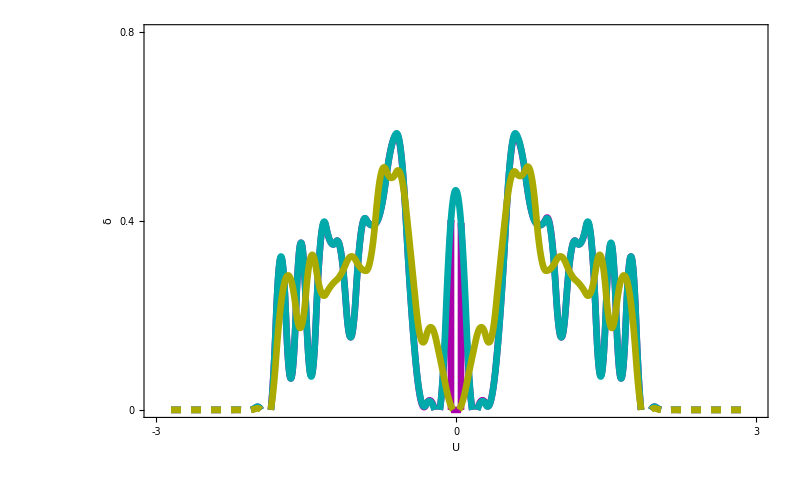

```mathematica
Show[
a0d8b0d5u1hist,a0d8b0d5u0hist,a0d8b0u0hist,
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.4,0.8},None},{{-3,0,3},None}},FrameTicksStyle->FontSize->50
]
```

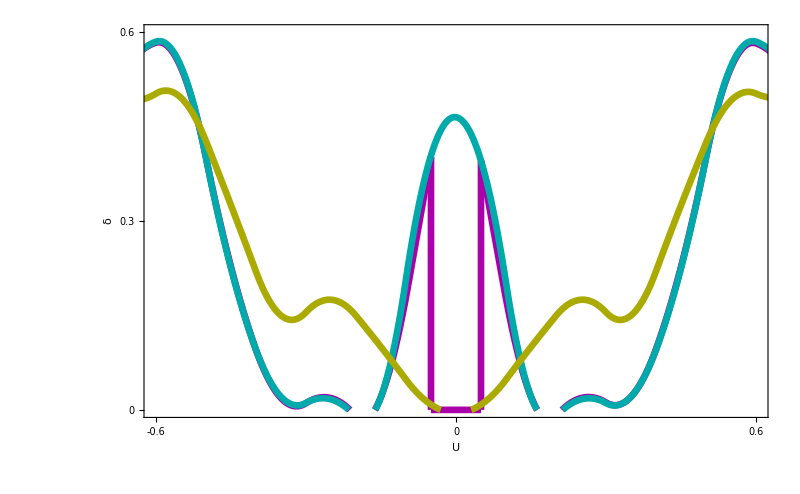

```mathematica
Show[
a0d8b0d5u1hist,a0d8b0d5u0hist,a0d8b0u0hist,
PlotRange->{{-0.6,0.6},{0,0.6}},
BaseStyle-> 18,Frame-> True,Axes-> False,
FrameLabel-> {"U","δ"},RotateLabel-> False,FrameStyle->{ {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}, {Directive[Black,AbsoluteThickness[4]]}},ImageSize->800,
FrameTicks->{{{0,0.3,0.6},None},{{-0.6,0,0.6},None}},FrameTicksStyle->FontSize->50
]
```